# MATHEMATICA : PRÁCTICA 2

Primera Parte
Desarrollar la simulación del procedimiento Stop & Wait

PUNTO 1

Estudiar la librería de representación de paquetes que se proporciona para identificar cómo se definen los parámetros de la transmisión y qué formato deben tener los paquetes que se proporcionan para la representación

```mathematica
(* GENERACIÓN DE PAQUETES *)
```

```mathematica
(* Cargamos la librería *)
```

```mathematica
(* Si ponemos << "directorio" nos cargaría también el directorio seleccionado *)
```

```mathematica
(* Para instalar la libreria ir a: File -> Install -> Package -> Source -> From File *)
```

```mathematica
Clear["Global'*"];
SetDirectory["F:\\3.TERCERO\\1.CUATRI\\PRM\\Mathematica\\Practica 3"];
```

SetDirectory::cdir: Cannot set current directory to "F:\\3.TERCERO\\1.CUATRI\\PRM\\Mathematica\\Practica 3".

```mathematica
Needs["drawTx`"]
```

```mathematica
(* EJEMPLO *)
```

```mathematica
(* Para representar los paquetes sobre una línea de tiempo *)
```

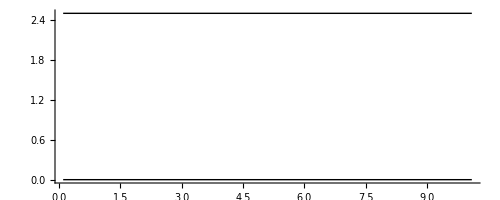

```mathematica
g=DrawWin[0.1,10,10]
```

```mathematica
(* Primer número -> tiempo en el que empieza el eje de tiempos
Segundo número -> longitud del eje de tiempos
Tercer número -> si pongo 10 cuenta de 0 a 9 paquetes *)
```

```mathematica
a={.2,.5,1,0,0};
```

```mathematica
(* Primer número -> tiempo inicial
Segundo número -> tiempo de inserción (lo que dura el paquete)
Tercer número -> número de secuencia
Cuarto número -> error
Quinto número -> número de retransmisiones *)
```

```mathematica
b={1,1,2,0,0};
```

```mathematica
(* Vamos a establecer los tiempos de propagación y supervisión *)
```

```mathematica
SetIniParDraw[0.5,0.1];
```

```mathematica
(* Primer número -> tiempo de propagación
Segundo número -> tiempo de supervisión *)
```

```mathematica
(* Visualizamos los paquetes *)
```

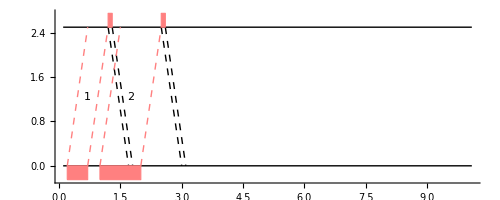

```mathematica
Show[g,DrawPacketTx[a],DrawPacketTx[b]]
```

```mathematica
(* Los dos paquetes se transmiten sin error *)
```

```mathematica
tprop=1;
```

```mathematica
tsup=0.1;
```

```mathematica
ti=a[[1]]+a[[2]]+2*tprop+tsup;
```

```mathematica
(* Cada paquete se introduce en la línea cuando el usuario llega a la misma : tinit *)
```

```mathematica
b={ti,1,2,0,0};
```

```mathematica
ti2=b[[1]]+b[[2]]+2*tprop+tsup;
```

```mathematica
c={ti2,1,3,2,0};
```

```mathematica
(* Mediante el Comando SetIniParDraw nos aseguramos que el siguiente paquete no se envíe hasta que no haya llegado la confirmación del anterior *)
```

```mathematica
SetIniParDraw[tprop,tsup];
```

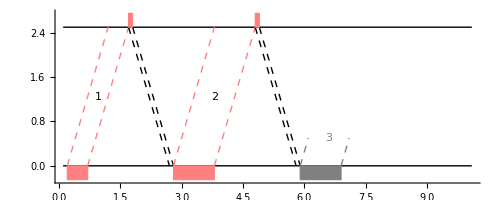

```mathematica
Show[g,DrawPacketTx[a],DrawPacketTx[b],DrawPacketTx[c]]
```

```mathematica
(* Al igual que en el caso anterior, los primeros dos paquetes se retransmiten correctamente *)
```

```mathematica
(* Esto sería lo que habría que repetir para hacer el protocolo Stop & Wait *)
```

PUNTO 2

Probar la representación de la librería para un caso particular de Stop & Wait sin errores y con tiempo de propagación 0. Posteriormente hacerlo proporcionando otros valores a ada parámetro.

```mathematica
(* STOP & WAIT *)
(* Algoritmo STOP & WAIT : si el paquete no tiene error se mete directamente a la lista. Si el paquete tiene error se mete en otro bucle hasta que se encuentre un nuevo paquete sin error *)
```

```mathematica
(* Definimos parámetros *)
```

```mathematica
nmax=1000;
```

```mathematica
landa=80;
```

```mathematica
mu=100;
```

```mathematica
(* tiemposEntreLlegadas *)
```

```mathematica
tiemposEntreLlegadas=Table[-1/landa*Log[RandomReal[]],{nmax}];
```

```mathematica
tiemposEntreLlegadas[[10;;20]]
```

{0.00756453,0.00425564,0.0013412,0.00761144,0.0154146,0.000582547,0.000794257,0.0256055,0.00589156,0.000955568,0.00118905}

```mathematica
(* tiemposDeServicio *)
```

```mathematica
tiemposDeServicio=Table[-1/mu*Log[RandomReal[]],{nmax}];
```

```mathematica
tiemposDeServicio[[10;;20]]
```

{0.00253829,0.0103904,0.00582924,0.0181758,0.00798382,0.0116218,0.000817394,0.00939084,0.0164017,0.00276736,0.0158211}

```mathematica
(* tiemposDeLlegadas *)
```

```mathematica
AcumSeries[list_]:=Module[{acum=0},
Map[(acum+=#)&,list]
];
```

```mathematica
tiemposDeLlegadas=AcumSeries[tiemposEntreLlegadas];
```

```mathematica
tiemposDeLlegadas[[10;;20]]
```

{0.181844,0.1861,0.187441,0.195052,0.210467,0.211049,0.211844,0.237449,0.243341,0.244296,0.245485}

```mathematica
(* Creamos la lista de paquetes usando los tiempos de llegada y tiempos de servicio *)
```

```mathematica
CreateList[arrivals_,service_,p_]:=
Module[{n=0},
MapThread[{#1,#2,n++,If[RandomReal[]<p,1,0],0}&,{arrivals,service}
]
];
```

```mathematica
listPack=CreateList[tiemposDeLlegadas,tiemposDeServicio,0.2];
```

```mathematica
listPack[[10;;20]]
```

{{0.181844,0.00253829,9,0,0},{0.1861,0.0103904,10,0,0},{0.187441,0.00582924,11,0,0},{0.195052,0.0181758,12,0,0},{0.210467,0.00798382,13,0,0},{0.211049,0.0116218,14,0,0},{0.211844,0.000817394,15,1,0},{0.237449,0.00939084,16,0,0},{0.243341,0.0164017,17,0,0},{0.244296,0.00276736,18,0,0},{0.245485,0.0158211,19,0,0}}

```mathematica
(* Primer término -> tiempo de llegada
Segundo término -> tiempo de servicio
Tercer término -> número de secuencia
Cuarto término -> error
Quinto término -> número de retransmisiones *)
```

```mathematica
SetIniParDraw[0.1,0];
```

```mathematica
g=DrawWin[3,3,10];
```

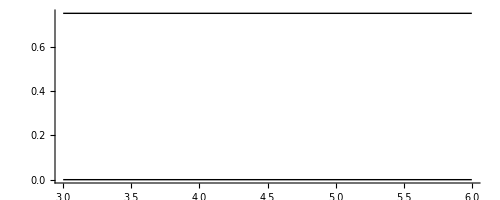

```mathematica
Show[g,Map[DrawPacketTx[#]&,listPack[[1;;20]]]]
```

```mathematica
(* Hacemos que haya retransmisiones cuando se produce error en los paquetes *)
```

```mathematica
(* El problema es que en esta simulación, las retransmisiones de los paquetes se solaparán *)
```

```mathematica
CreateTx[arrivals_,service_,p_]:=Module[{n=0},
GetRtxPacket[arr_,srv_,prob_]:=(
lstPck={}; 
nrtx=0;
(* Creamos una lista de paquetes vacía que iremos rellenando e inicializo el número de retransmisiones *)
While[If[RandomReal[]<prob,1,0]==1, (* Mientras haya error *)
AppendTo[lstPck,{arr,srv,n,1,nrtx++}];
]; (* Reenviamos el mismo paquete *)
(* AppendTo: añade un elemento, un paquete, al final de una lista *)
AppendTo[lstPck,{arr,srv,n++,0,nrtx++}];
lstPck (* Para que me devuelva la lista de paquetes *)
);
Flatten[MapThread[GetRtxPacket[#1,#2,p]&,{arrivals,service}],1]
];
```

```mathematica
(* MapThread: permite hacer un Map con más de una lista. Tengo que aplicarle el Flatten porque se queda todo agrupado en un grupo *)
(* GetRtxPacket: While -> mientras haya error (<prob), añado a la lista 'lstPck' el paquete con el mismo número de secuencia, error=1 y el número de retransmisiones 'nrtx' incrementado. Los 3 parámetros que le paso son los mismos que los de la función CreateTx, pero tengo que pasárselos también porque sino no funciona.
Al salir del While, añado a la lista 'lstPck' el paquete ya correcto con error=0, número de secuencia incrementado y número de retransmisiones incrementado. Hago que esta función me devuelva la lista de paquetes *)
(* Sería mejor hacer la función GetRtxPacket[] con un NestWhileList[] *)
```

```mathematica
listPack=CreateTx[tiemposDeLlegadas,tiemposDeServicio,0];
```

```mathematica
listPack[[10;;20]]
```

{{0.181844,0.00253829,9,0,0},{0.1861,0.0103904,10,0,0},{0.187441,0.00582924,11,0,0},{0.195052,0.0181758,12,0,0},{0.210467,0.00798382,13,0,0},{0.211049,0.0116218,14,0,0},{0.211844,0.000817394,15,0,0},{0.237449,0.00939084,16,0,0},{0.243341,0.0164017,17,0,0},{0.244296,0.00276736,18,0,0},{0.245485,0.0158211,19,0,0}}

```mathematica
Manipulate[
Show[DrawWin[tw,ww,10],
Map[DrawPacketTx[#]&,SelectPacketInWin[listPack]]
],
{tw,0.01,10},{ww,0.01,10}]
```

```mathematica
(* Hay que corregir los tiempos de llegada de cada paquete con el 'checkTime' para que no se solapen con las retransmisiones *)
```

```mathematica
CreateTx[arrivals_,service_,p_]:=
Module[{n=0,checkTime=0,tp=0.1,ts=0},
GetRtxPacket[arr_,srv_,prob_]:=(
lstPck={}; 
nrtx=0;
If[arr>checkTime,checkTime=arr];
While[If[RandomReal[]<prob,1,0]==1,
AppendTo[lstPck,{checkTime,srv,n,1,nrtx++}];
checkTime+=2*tp+ts+srv;
];
AppendTo[lstPck,{checkTime,srv,n++,0,nrtx++}];
checkTime+=2*tp+ts+srv;
lstPck 
);
Flatten[MapThread[GetRtxPacket[#1,#2,p]&,{arrivals,service}],1]
];
```

```mathematica
(* Añadimos a la función el valor 'checkTime' para saber cuándo un paquete es ya correcto tras las retransmisiones necesarias, el tiempo de propagación, y el tiempo de supervisión *)
(* A 'checkTime' le sumamos cada vez el tiempo de ack y el tiempo de servicio -> cada 'checkTime' es el tiempo desde que A inserta un paquete en la línea, va hasta B, y A recibe la confirmación de B (después de todas las retransmisiones, si las hay). Por eso, cuando hacemos el AppendTo para insertar un paquete, el tiempo de inserción de paquete será el 'checkTime' calculado previamente, es decir, donde acaba la confimación del anterior paquete *)
```

```mathematica
listPack=CreateTx[tiemposDeLlegadas,tiemposDeServicio,0.4];
```

```mathematica
listPack[[10;;20]]
```

{{1.86239,0.0071219,6,1,1},{2.06951,0.0071219,6,0,2},{2.27663,0.000390562,7,0,0},{2.47702,0.00236108,8,0,0},{2.67938,0.00253829,9,0,0},{2.88192,0.0103904,10,0,0},{3.09231,0.00582924,11,0,0},{3.29814,0.0181758,12,1,0},{3.51632,0.0181758,12,0,1},{3.73449,0.00798382,13,1,0},{3.94248,0.00798382,13,0,1}}

```mathematica
Manipulate[
Show[DrawWin[tw,ww,10],
Map[DrawPacketTx[#]&,SelectPacketInWin[listPack]]
],
{tw,0.01,10},{ww,0.1,10}]
```

```mathematica
(* Otro ejemplo *)
```

```mathematica
listPack[[10;;200]];
SetIniParDraw[0.1,0]
Manipulate[
Show[DrawWin[tw,ww,8],
Map[DrawPacketTx[#]&,SelectPacketInWin[listPack]
]
]
,{tw,0.01,10},{ww,0.1,10}
]
```

Segunda Parte

Comparar rendimientos con valores teóricos y de diferentes simulaciones

PUNTO 4

Dibujar la evolución del throughput a lo largo de la transmisión

```mathematica
(* Cogemos el número de paquetes y lo dividimos entre el tiempo -> dividimos el 3.ba parámetro entre el 1.ba *)
```

```mathematica
(* Lista de valores instantáneos del throughput *)
```

```mathematica
ThLista[lst_]:=Map[(#[[3]]/#[[1]])&,lst];
```

```mathematica
thPaquete=ThLista[listPack];
```

```mathematica
thPaquete[[5;;10]]
```

{3.63765,3.89375,3.2403,3.46833,3.62479,3.22167}

```mathematica
(* Gráfica de la evolución del Throughpul *)
```

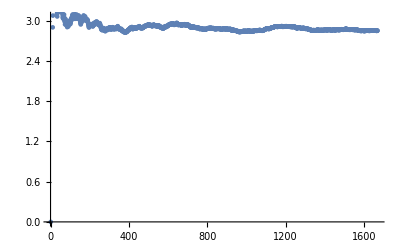

```mathematica
ListPlot[thPaquete]
```

```mathematica
(* Si queremos saber dónde converge la lista, tendremos que coger el último throughput (el throughput es el último número porque es como el resumen de todo lo que ha pasado), y para ello tendremos que utilizar el último tiempo *)
```

```mathematica
(* Seleccionamos el último paquete de la lista *)
```

```mathematica
ThFinal[lst_]:=Last[lst];
```

```mathematica
Last[listPack]
```

{350.391,0.00444727,999,0,0}

```mathematica
(* El thoughput lo conseguimos dividiendo el número de secuencia (3) entre el tiempo inicial (1) *)
```

```mathematica
lastTh=Last[listPack][[3]]/Last[listPack][[1]]
```

2.8511

```mathematica
(* Otras maneras de hacerlo *)
```

```mathematica
ThFinal1[lst_]:=Last[ThLista[lst]];
```

```mathematica
lastTh1=ThFinal1[listPack]
```

2.8511

```mathematica
ThFinal2[lst_]:=(a=Last[lst];a[[3]]/a[[1]]);
```

```mathematica
lastTh2=ThFinal2[listPack]
```

2.8511

PUNTO 6

Hacer gráficas de esos parámetros variando cada uno de ellos, a, p o ro

```mathematica
(* Ahora vamos a representar las gráficas del throughput según varios parámetros *)
(* Una ro muy baja nunca va a llegar a los límites *) 
(* Tenemos que estudiar la variación del punto de trabajo según los valores de los parámetros ro y a *)
```

```mathematica
(* Inicializamos los parámetros *)
```

λ=80;
μ=100;
ρ=λ/μ; 
λmax=(1-p)/(a*ti);
a: [0,10], p: [0,1], ti: [0,100] ???, ρ (intensidad de tráfico): [0.1,1]

```mathematica
(* Función del throughput máximo teórico potencial (la curva límite) *)
```

```mathematica
ThMaxTH[a_,tI_,p_]:=((1-p)/(a*tI));
```

```mathematica
(* Representación del throughput en función de ro *)
```

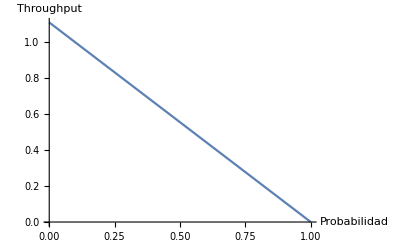

```mathematica
Plot[ThMaxTH[a=3,tI=0.3,pr],{pr,0,1},
AxesLabel-> {"Probabilidad","Throughput"}]
```

```mathematica
(* Representación del throughput en función de a *)
```

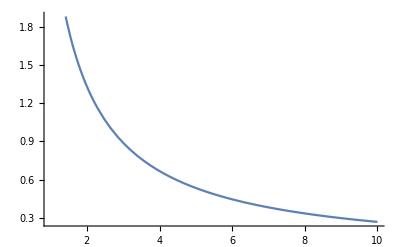

```mathematica
Plot[ThMaxTH[ar,tI=0.3,p=0.2],{ar,1,10}]
```

a-1=tack/tI
tack=2*tp

```mathematica
(* Modificamos la función antigua CreateTx añadiendo tp a los parámetros iniciales *)
```

```mathematica
CreateTx2[arrivals_,service_,p_,tp_]:=Module[{n=0,checkTime=0,ts=0},
GetRtxPacket[arr_,srv_,prob_]:=(
lstPck={};nrtx=0;
If[arr>checkTime,checkTime=arr];
While[(If[RandomReal[]<prob,1,0])==1,
AppendTo[lstPck,{checkTime,srv,n,1,nrtx++}]
];
checkTime+=2*tp+ts+srv;
AppendTo[lstPck,{checkTime,srv,n++,0,nrtx++}];
checkTime+=2*tp+ts+srv;
lstPck
);
Flatten[MapThread[GetRtxPacket[#1,#2,p]&,{arrivals,service}],1]
];
```

```mathematica
LaunchSim[ro_,mu_,p_,a_,npack_]:=
CreateTx2[
AcumSeries[
Table[-1/(ro*mu)*Log[RandomReal[]],{npack}] (* arrivals *)
], 
Table[-1/mu*Log[RandomReal[]],{npack}] (* services *)
,p,(a-1)/(2*mu)
] ;
```

```mathematica
(* Utilizamos una de las funciones del throughput que hemos calculado el PUNTO 4 *)
```

```mathematica
ThFinal2[lst_]:=(a=Last[lst];a[[3]]/a[[1]]);
```

```mathematica
ThSim[ro_,mu_,p_,a_,npack_]:=ThFinal2[LaunchSim[ro,mu,p,a,npack]];
```

```mathematica
b=LaunchSim[0.2,100,0.2,2,1000];
```

```mathematica
b[[10;;20]]
```

{{0.377071,0.00267905,8,0,0},{0.39978,0.0000302545,9,0,0},{0.427741,0.0079304,10,0,0},{0.446873,0.0150807,11,1,0},{0.471954,0.0150807,11,0,1},{0.497035,0.00692157,12,1,0},{0.497035,0.00692157,12,1,1},{0.513957,0.00692157,12,0,2},{0.555109,0.00766409,13,1,0},{0.572773,0.00766409,13,0,1},{0.607999,0.00756126,14,0,0}}

```mathematica
ThSim[0.2,100,0.2,2,1000]
```

20.148

```mathematica
(* Ahora vamos a representar las gráficas anteriores mediante un Manipulate, para ir viendo las variaciones del punto de trabajo según los cambios de valores de los parámetros *)
```

```mathematica
Manipulate[
Show[
Plot[ThMaxTH[a,tI=1/mu,pr],{pr,0,1}],
Graphics[{PointSize[Large],Red,
Point[{ro,ThSim[ro,mu,p,a,npack]}]}
]
]
,{a,1,10,1},{p,0,1},{ro,0.1,1},{mu,10,100},{npack,{100,1000,5000}}]
```

```mathematica
Manipulate[
Show[
Plot[ThMaxTH[ar,tI=1/μ,p],{ar,1,10}],
Graphics[{PointSize[Large],Red,Point[{a,ThSim[ρ,μ,p,a,npack]}]}]
],
{a,1,10,1},{p,0,1},{ρ,0.1,1},{μ,10,100},{npack,{100,1000,5000}}]
```

Tercera Parte

Desarrollar la simulación del procedimiento GO-BACK-N

PUNTO 8

Resolver la simulación para GO-BACK-N. Inicialmente se puede hacer la simplificación de no considerar las transmisioes dentro de la ventana con error en la trama

```mathematica
(* GO-BACK-N *)
```

```mathematica
(* Volvemos a calcular todos los parámetros que hemos calculado para la simulación del procedimiento Stop & Wait *)
```

```mathematica
nmax=1000;
landa=80;
mu=100;
```

```mathematica
tiemposEntreLlegadas=Table[-1/landa*Log[RandomReal[]],{nmax}];
```

```mathematica
tiemposEntreLlegadas[[10;;20]]
```

{0.0024699,0.0110058,0.0320415,0.00330095,0.0405389,0.0127513,0.00139517,0.0184223,0.008619,0.00128875,0.0664906}

```mathematica
tiemposDeServicio=Table[-1/mu*Log[RandomReal[]],{nmax}];
```

```mathematica
tiemposDeServicio[[10;;20]]
```

{0.00727211,0.000613322,0.0052124,0.0293029,0.00481653,0.0031037,0.0127016,0.00406273,0.0142331,0.0146856,0.00180919}

```mathematica
AcumSeries[list_]:=Module[{acum=0},
Map[(acum+=#)&,list]
]
```

```mathematica
tiemposDeLlegadas=AcumSeries[tiemposEntreLlegadas];
```

```mathematica
tiemposDeLlegadas[[10;;20]]
```

{0.0943836,0.105389,0.137431,0.140732,0.181271,0.194022,0.195417,0.21384,0.222459,0.223747,0.290238}

```mathematica
(* GO-BACK-N *)
```

```mathematica
CreateTxGBN[arrivals_,service_,p_]:=
Module[{n=0,nrtx=0,checkTime=0,ts=0,tp=0.1,lstPck={}},
GetRtxPacket[arr_,srv_,prob_]:=(
lstPck={};nrtx=0;
If[arr>checkTime,checkTime=arr];
While[(If[RandomReal[]<prob,1,0])==1,
AppendTo[lstPck,{checkTime,srv,n,1,nrtx++}];
checkTime+=2*tp+ts+srv;
];
AppendTo[lstPck,{checkTime,srv,n++,0,nrtx++}];
checkTime+=srv;
lstPck
);
Flatten[MapThread[GetRtxPacket[#1,#2,p]&,{arrivals,service}],1]
];
```

```mathematica
listPackGBN=CreateTxGBN[tiemposDeLlegadas,tiemposDeServicio,0.4];
```

```mathematica
listPackGBN[[10;;20]]
```

{{0.775579,0.00852928,6,1,1},{0.984108,0.00852928,6,1,2},{1.19264,0.00852928,6,1,3},{1.40117,0.00852928,6,0,4},{1.4097,0.00194025,7,0,0},{1.41164,0.0200198,8,0,0},{1.43166,0.00727211,9,0,0},{1.43893,0.000613322,10,1,0},{1.63954,0.000613322,10,0,1},{1.64015,0.0052124,11,0,0},{1.64537,0.0293029,12,1,0}}

```mathematica
SetIniParDraw[0.1,0];
```

```mathematica
Manipulate[
Show[DrawWin[tw,ww,10],
Map[DrawPacketTx[#]&,SelectPacketInWin[listPackGBN]]
],
{tw,0.01,10},{ww,0.01,10}]
```